## Prepare

```mathematica
imgsize=700;
imgpadding={{70, 20}, {50, 10}};
```

Always use the first element in the vector to be the component of small eigenvalue.

```mathematica
$MachinePrecision
```

15.9546

### Modules

Making Plots

```mathematica
pltNorm[sol_,c1_,c2_,start_,end_]:=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2[x]]^2/.sol[[1]]],{x,start,end},PlotRange->All,ImageSize->imgsize,Frame->True];
```

Plot transitioin Probabilities: Probability of c2

```mathematica
pltProb[sol_,c2_,c1_,start_,end_,pltLabel_,frameLabel_]:=Plot[Evaluate[Abs[c2[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]]^2)/.sol[[1]]],{x,start,end},PlotRange->All,PlotLabel->pltLabel,ImageSize->imgsize,Frame->True,FrameLabel->frameLabel,ImagePadding->imgpadding,PerformanceGoal->"Quality"];
```

Rotation matrices

Rotation from vacuum to instantaneous matter basis

```mathematica
vac2instRotation[a0_,a1_,tv_]:=Module[{thetaxConst,alpha0=a0,alpha1=a1,thetav=tv},thetaxConst=ArcSin[Sin[2thetav]/(√(1+(alpha0+alpha1)^2-2(alpha0+alpha1)Cos[2thetav]))]/2;{{Cos[thetav-thetaxConst],Sin[thetav-thetaxConst]},{-Sin[thetav-thetaxConst],Cos[thetav-thetaxConst]}}]
```

Pauli matrices

```mathematica
sigma3=PauliMatrix[3];
sigma1=PauliMatrix[1];
```

Conversion from length (km) to energy (eV): 197.33 MeV*fm=1 =>

```mathematica
hbarc=197.3269788
```

197.327

```mathematica
km2eV[km_]:=Module[{length=km},(hbarc*10^6)/(km*10^(18))]
eV2km[eV_]:=Module[{energy=eV},(hbarc*10^(-18))/(eV*10^(-6))]
```

#### Paramters

Paramters are grabbed from Kneller’s paper

#### Initial Condition

In (averaged) matter basis

```mathematica
N@Pi/4
```

0.785398

```mathematica
θv=0.573(*Pi/4-0.573/180*Pi*)
energy=20*10^6; (* eV *)
deltam2=3*10^(-3); (* eV^2 *)
(* The following are calculated *)
omegav=deltam2/(2energy); (* 7.5*10^(-11) *) (*eV, delta^2m= 3*10^(-3)eV^2, E =20MeV*)
α0=Cos[2θv]
(* α0=0;*)
(*α1=0;*)
α1=0.1α0;
(*β=0.937*) β=(2*km2eV[5.26])/omegav
phasem=0;
```

0.573

0.412135

1.00039

```mathematica
θm=ArcTan[Sin[θv]/(Cos[θv]-α0)]
```

0.902364

The initial condition in matter basis

```mathematica
initAM={1,0}
```

{1,0}

Rotate to vacuum eigenbasis

```mathematica
vac2instRotation[α0,0,θv]//MatrixForm
initVac=Transpose[vac2instRotation[α0,0,θv]].initAM
```

(0.977528 | -0.210805
0.210805 | 0.977528)

{0.977528,-0.210805}

```mathematica
endpoint=(6*10^9/5)*10^(-5)(* omegav/km2eV[10^4];*)
%//N
```

12000

12000.

```mathematica
N@km2eV[10^(10-2-3)]/omegav
```

0.0000263103

#### Test of Defined Functions and Parametser + Check Numbers

```mathematica
"σ3 is "MatrixForm@sigma3
"σ1 is "MatrixForm@sigma1
```

σ3 is  (1 | 0
0 | -1)

σ1 is  (0 | 1
1 | 0)

Test Rotation

```mathematica
vac2instRotationTest=Module[{θv=ArcSin@√0.307},Grid[{{"Zero Matter Potential: "<>ToString@vac2instRotation[0,0,θv]},{"MSW Resonance: "<>ToString@vac2instRotation[Cos[2*θv],0,θv]}}]]
```

Zero Matter Potential: {{1., 0.}, {0., 1.}}
MSW Resonance: {{0.980433, -0.196852}, {0.196852, 0.980433}}

Test Unit convsersion

```mathematica
km2eV[10^(-18)]
eV2km[10^6]
```

1.97327×10^8

1.97327×10^-16

#### Check Numbers

```mathematica
ArcSin[Sin[2θv]/(√(1+(α0+α1)^2-2(α0+α1)Cos[2θv]))]/2
Sin[2ArcTan[Sin[2θv]/(Cos[2θv]-α0)]/2]^2
```

0.762797

Power::infy: Infinite expression 1/0. encountered.

Indeterminate

```mathematica
omegav//N
```

7.5×10^-11

```mathematica
(6/omegav)*10^(-7)*197/Pi//N
```

501656.

```mathematica
1/km2eV[1]//N
```

5.06773×10^9

```mathematica
θv*Pi/180
```

0.0100007

```mathematica
(2Pi/omegav*√(1+α0^2-2α0 Cos[2θv]))*10^(-7)*197
```

1.5037×10^6

```mathematica
(100/omegav)*10^(-7)*197//N
```

2.62667×10^7

### Some Conversions and Comparisons

#### A Table of All Parameters

```mathematica
Grid[{{"-","θ_V","Δm^2/eV^2","E/MeV","ω_V/eV","λ_m/km","C_*","Phase of Matter Profiles"},{"Kneller",0.573,N@3*10^(-3),20,N@3*10^(-3)/(2*20*10^6),5.27,0.1,"η"},{"Now",θv,N@deltam2,N@energy*10^(-6),N@omegav,eV2km[β omegav/2],α1/α0,phasem}},Frame->All]
```

- | θ_V | Δm^2/eV^2 | E/MeV | ω_V/eV | λ_m/km | C_* | Phase of Matter Profiles
Kneller | 0.573 | 0.003 | 20 | 7.5×10^-11 | 5.27 | 0.1 | η
Now | 0.573 | 0.003 | 20. | 7.5×10^-11 | 5.26 | 0.1 | 0

#### Numerical Check

Frequencies/wavelength in Kneller’s paper

Vacuum

```mathematica
N@omegav
```

7.5×10^-11

Vacuum Wavelegth to km (Using Kneller’s convention that wavelength=2/)

```mathematica
eV2km[omegav]*2
```

5.26205

Matter frequency

```mathematica
omegam=omegav*√(α0^2+1-2α0 Cos[2θv])
```

6.83342×10^-11

Corresponding wavelength

```mathematica
eV2km[omegam]*2
```

5.77535

Wavelength of transition probability in Kneller’s resonance

```mathematica
(6*10^9/5)*10^(-5)
```

12000

This corresponds to many vacuum lengths

```mathematica
%/(eV2km[omegav]*2)
```

2280.48

## Defining System

Hamiltonian in Vacuum basis of a system is

```mathematica
hVac[matter_,x_]:=Module[{lambda=matter},-1/2 sigma3+lambda/2 Cos[2*θv]sigma3+lambda/2 Sin[2*θv]sigma1]
```

## Equation Solving

### Sovling Schrodinger equation Hamiltonian

The normalized Hamiltonian in vacuum basis is

```mathematica
hVac[α0+α1*Sin[β*x+phasem],x]
```

{{-0.5+0.206068 (0.412135+0.0412135 Sin[1.00039 x]),0.+0.455561 (0.412135+0.0412135 Sin[1.00039 x])},{0.+0.455561 (0.412135+0.0412135 Sin[1.00039 x]),0.5-0.206068 (0.412135+0.0412135 Sin[1.00039 x])}}

```mathematica
hamilVac[x_]=hVac[α0+α1*Sin[β*x+phasem],x]
```

{{-0.5+0.206068 (0.412135+0.0412135 Sin[1.00039 x]),0.+0.455561 (0.412135+0.0412135 Sin[1.00039 x])},{0.+0.455561 (0.412135+0.0412135 Sin[1.00039 x]),0.5-0.206068 (0.412135+0.0412135 Sin[1.00039 x])}}

```mathematica
waveVac0[x_]={waveVac01[x],waveVac02[x]};
solVac0=NDSolve[{I D[waveVac0[x],x]==hamilVac[x].waveVac0[x],waveVac0[0]==initVac},waveVac0[x],{x,0,endpoint}]
```

{{waveVac01[x]→InterpolatingFunction[{{0., 12000.}}, <>][x],waveVac02[x]→InterpolatingFunction[{{0., 12000.}}, <>][x]}}

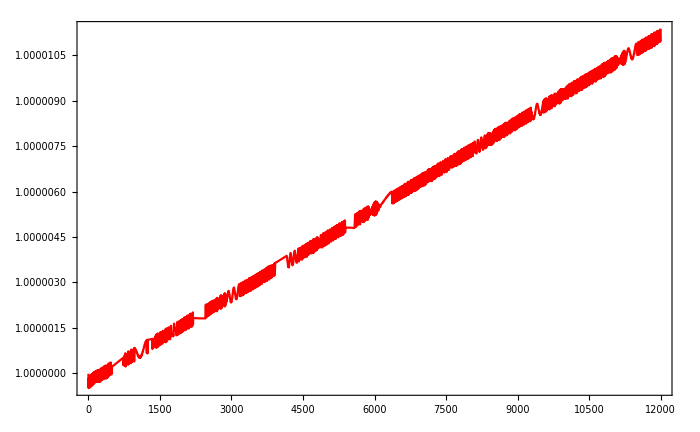

```mathematica
Plot[Evaluate[Abs[waveVac01[x]]^2+Abs[waveVac02[x]]^2/.solVac0[[1]]],{x,0,endpoint},PlotStyle->{Blue,Red},PlotRange->All,ImageSize->imgsize,Frame->True]
```

```mathematica
pltNorm[solVac0,waveVac01,waveVac02,0,endpoint];
```

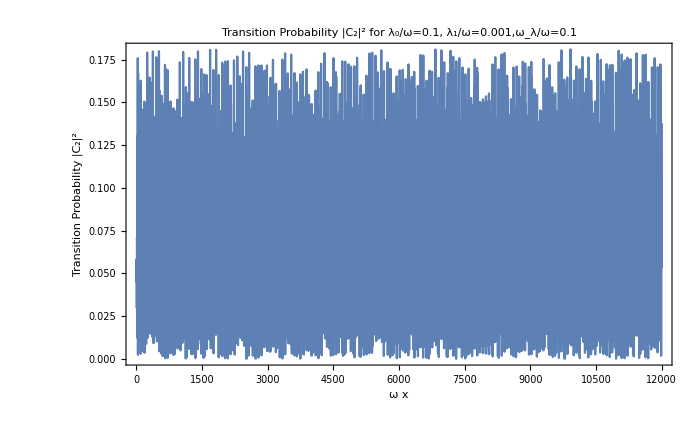

```mathematica
pltProb[solVac0,waveVac02,waveVac01,0,endpoint,"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",{"ω x","Transition Probability |C_2|^2"}]
```

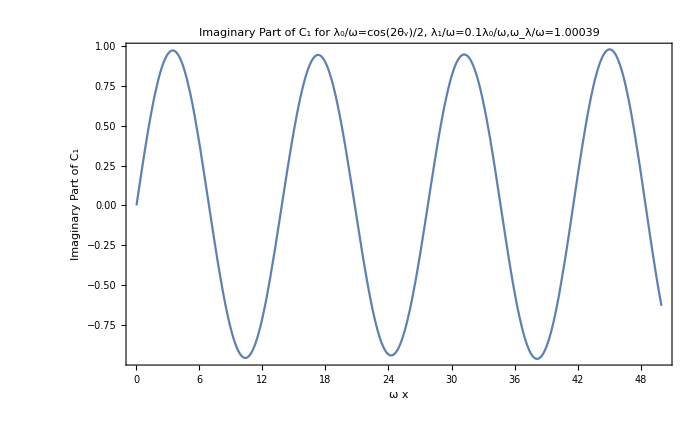

```mathematica
Plot[Evaluate[Im[waveVac01[x]]]/.solVac0[[1]],{x,0,50},PlotRange->All,PlotLabel->"Imaginary Part of C_1 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Imaginary Part of C_1"},ImagePadding->imgpadding]
```

### Rotate to Matter Basis

Wavefunction in matter basis is

```mathematica
instWaveFunction[x_]=vac2instRotation[α0,0,θv].{waveVac01[x],waveVac02[x]}/.solVac0[[1]];
```

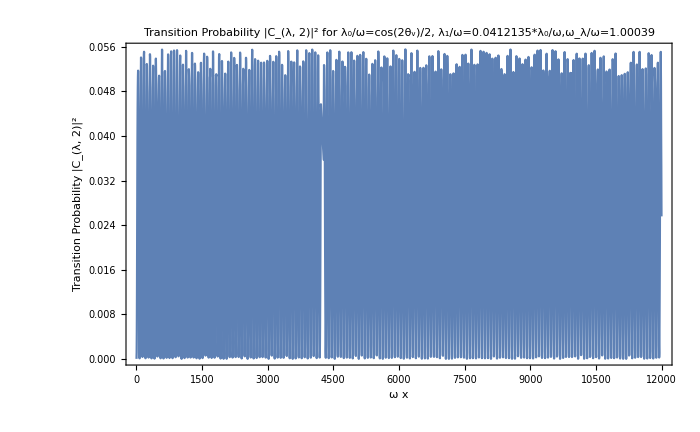

```mathematica
probInstHeavy=Plot[Abs[instWaveFunction[x][[2]]]^2/(Abs[instWaveFunction[x][[1]]]^2+Abs[instWaveFunction[x][[2]]]^2),{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω="<>ToString[α1]<>"*λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

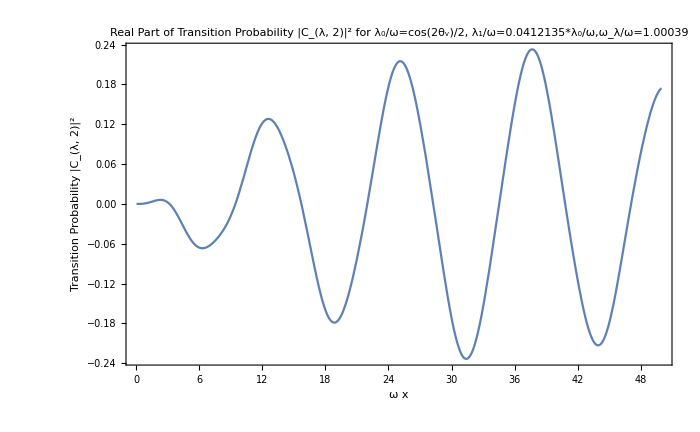

```mathematica
instHeavyRe=Plot[Re[instWaveFunction[x][[2]]],{x,0,50},PlotRange->All,PlotLabel->"Real Part of Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω="<>ToString[α1]<>"*λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

### Flavor Basis

```mathematica
instWaveFunctionf[x_]={{Cos[θv],Sin[θv]},{-Sin[θv],Cos[θv]}}.{waveVac01[x],waveVac02[x]}/.solVac0[[1]]
```

{0.542155 InterpolatingFunction[{{0., 12000.}}, <>][x]+0.840278 InterpolatingFunction[{{0., 12000.}}, <>][x],0.840278 InterpolatingFunction[{{0., 12000.}}, <>][x]-0.542155 InterpolatingFunction[{{0., 12000.}}, <>][x]}

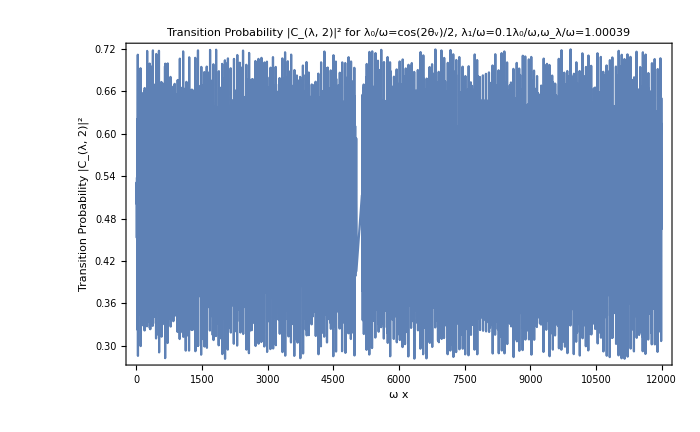

```mathematica
probf=Plot[Abs[instWaveFunctionf[x][[2]]]^2/(Abs[instWaveFunctionf[x][[2]]]^2+Abs[instWaveFunctionf[x][[1]]]^2),{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

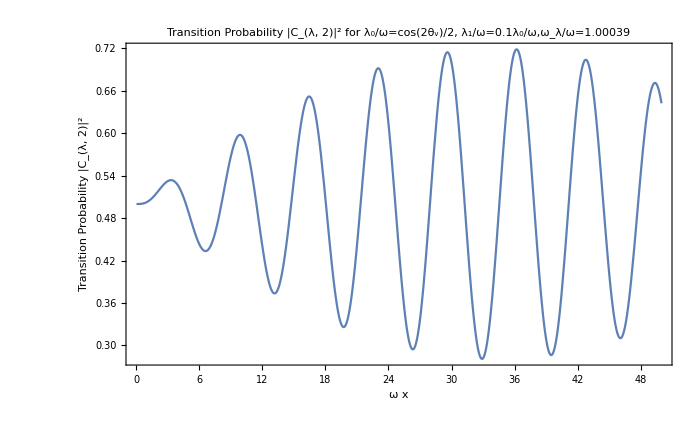

```mathematica
Plot[Abs[instWaveFunctionf[x][[2]]]^2/(Abs[instWaveFunctionf[x][[2]]]^2+Abs[instWaveFunctionf[x][[1]]]^2),{x,0,50},PlotRange->All,PlotLabel->"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

## Calculate in Matter Basis Directly

The calculation can be done in averaged matter basis directly.

Hamiltonian in (averaged) Matter basis is

```mathematica
hamilAM[lambda_,x_]:=vac2instRotation[α0,0,θv].hVac[lambda,x].Transpose[vac2instRotation[α0,0,θv]]//FullSimplify
```

Test this function

```mathematica
hamiltonianAM=hamilAM[α0+α1*Sin[β*x],x]
```

{{-0.455561+3.07065×10^-10 Sin[1.00039 x],6.78839×10^-9+0.0206068 Sin[1.00039 x]},{6.78839×10^-9+0.0206068 Sin[1.00039 x],0.455561-3.07065×10^-10 Sin[1.00039 x]}}

System to be solved is the Schrodinger equation

```mathematica
waveAM[x_]={waveAM1[x],waveAM2[x]};
```

```mathematica
solAM=NDSolve[{I D[waveAM[x],x]==hamiltonianAM.waveAM[x],waveAM[0]==initAM},waveAM[x],{x,0,endpoint}];
```

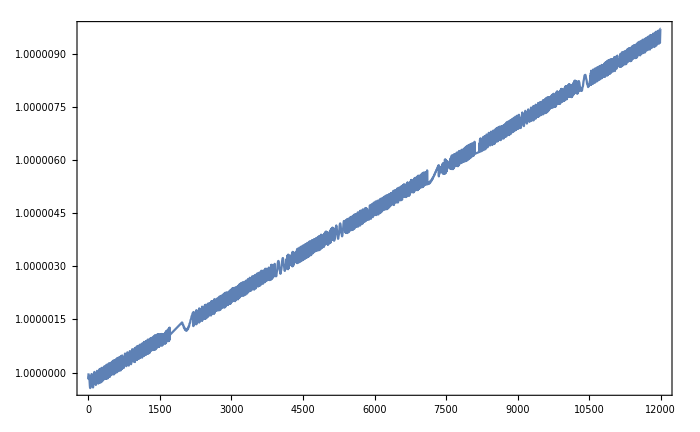

```mathematica
pltNorm[solAM,waveAM1,waveAM2,0,endpoint]
```

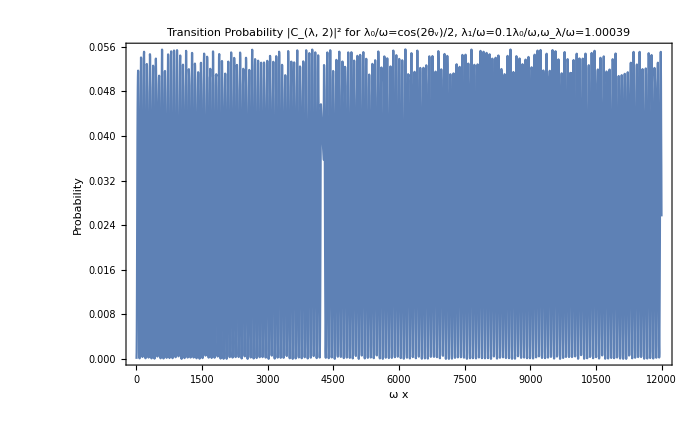

```mathematica
pltProb112=pltProb[solAM,waveAM2,waveAM1,0,endpoint,"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[β],{"ω x","Probability"}]
```

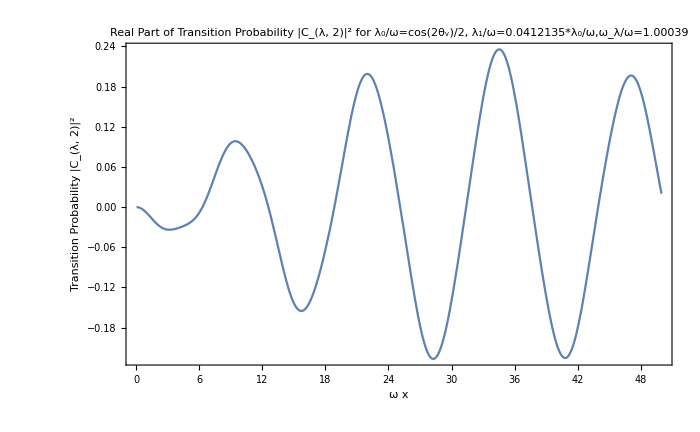

```mathematica
instHeavy2Re=Plot[Im[waveAM[x][[2]]]/.solAM,{x,0,50},PlotRange->All,PlotLabel->"Real Part of Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω="<>ToString[α1]<>"*λ_0/ω,ω_λ/ω="<>ToString[β],ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_(λ, 2)|^2"},ImagePadding->imgpadding]
```

```mathematica
Sin[2Pi x]
```

Sin[2 π x]

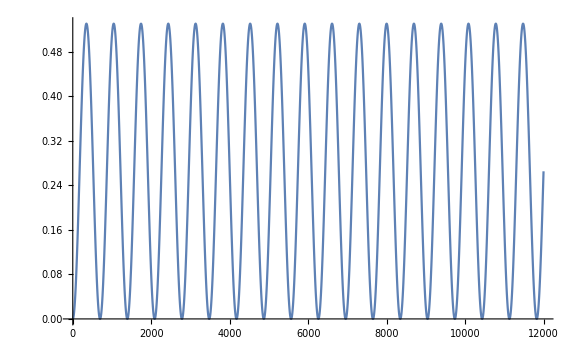

```mathematica
Plot[0.53Sin[2Pi (2Pi x)/omegav km2eV[2.3*10^4]]^2,{x,0,endpoint},ImageSize->Large]
```

### Scanning Parameters

```mathematica
testrangestart = 0
testrangeend=endpoint
Manipulate[pltProb[NDSolve[{I D[waveAM[x],x]==hamilAM[α0+α1*Sin[β*x],x].waveAM[x],waveAM[0]==initAM},waveAM[x],{x,testrangestart,testrangeend}],waveAM2,waveAM1,testrangestart,testrangeend,"Transition Probability |C_(λ, 2)|^2 for λ_0/ω=cos(2θ_v)/2, λ_1/ω=0.1λ_0/ω,ω_λ/ω="<>ToString[beta],{"ω x","Probability"}],{beta,0.7,If[wide,5,1.0],0.01},{{wide,False,"Wide Range"},{False,True}}]
```

0

12000

## Parametric Resonance

```mathematica
endpointCW=endpoint;
initCW={1,0};
```

#### Theory

Define the variables needed

```mathematica
lambdacw={100α0,10α0}
periodscw={20,0.15685493819720583}
factcw={√((lambdacw[[1]])^2+1-2(lambdacw[[1]])Cos[2θv]),√((lambdacw[[2]])^2+1-2(lambdacw[[2]])Cos[2θv])}
omegacw=factcw
phicw=omegacw*periodscw/2
nvec={{Sin[2θv]/factcw[[1]],0,-(Cos[2θv]-lambdacw[[1]])/factcw[[1]]},{Sin[2θv]/factcw[[2]],0,-(Cos[2θv]-lambdacw[[2]])/factcw[[2]]}}
rcw=Cos[phicw[[1]]]Cos[phicw[[2]]]-Sin[phicw[[1]]]Sin[phicw[[2]]](nvec[[1]].nvec[[2]])
xicw=ArcCos[rcw]
```

{41.2135,4.12135}

{20,0.156855}

{40.8116,3.81948}

{40.8116,3.81948}

{408.116,0.299552}

{{0.0223251,0,0.999751},{0.238546,0,0.971131}}

0.99795

0.0640362

```mathematica
iso={Sin[phicw[[1]]Cos[phicw[[2]]]] Sin[2θv]/factcw[[1]]+Cos[phicw[[1]]]Sin[phicw[[2]]] Sin[2θv]/factcw[[2]],-Sin[phicw[[1]]]Sin[phicw[[2]]](Sin[2θv]/factcw[[1]](Cos[2θv]-lambdacw[[2]])/factcw[[2]]-(Cos[2θv]-lambdacw[[1]])/factcw[[1]] Sin[2θv]/factcw[[2]]),-Sin[phicw[[1]]]Cos[phicw[[2]]](Cos[2θv]-lambdacw[[1]])/factcw[[1]]-Cos[phicw[[1]]]Sin[phicw[[2]]](Cos[2θv]-lambdacw[[2]])/factcw[[2]]}
```

{0.0757919,0.0183841,0.}

```mathematica
-Sin[phicw[[1]]]Cos[phicw[[2]]](Cos[2θv]-lambdacw[[1]])/factcw[[1]]
-Cos[phicw[[1]]]Sin[phicw[[2]]](Cos[2θv]-lambdacw[[2]])/factcw[[2]]
```

-0.274487

0.274487

```mathematica
probabilityCWTh[p_]=(1-iso[[3]]^2/Abs[iso.iso])Sin[p*xicw]^2
```

1. Sin[0.0640362 p]^2

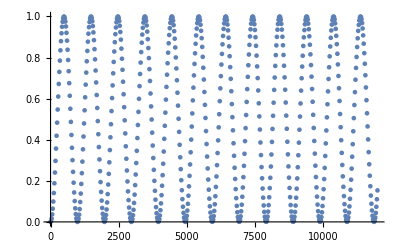

```mathematica
cwTh=ListPlot[Table[{num*(Total@periodscw),probabilityCWTh[num]},{num,0,Floor[endpointCW/(Total@periodscw)]}]]
```

#### Numerical

In vacuum basis, castle wall potential is

```mathematica
castleWall[lambda1_,lambda2_,period1_,period2_,x_]:=Piecewise[{{lambda1,0≤Mod[x,period1+period2]<period1},{lambda2,period1≤Mod[x,period1+period2]<period1+period2}}]
```

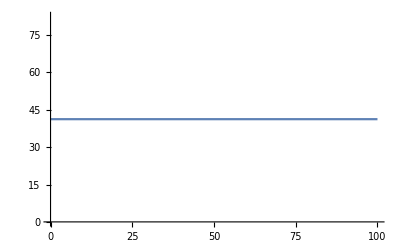

```mathematica
Plot[castleWall[lambdacw[[1]],lambdacw[[1]],periodscw[[1]],periodscw[[2]],x],{x,0,100}]
```

Parametric resonance Hamiltonian is

```mathematica
cwPotential[x_]=castleWall[lambdacw[[1]],lambdacw[[2]],periodscw[[1]],periodscw[[2]],x]
```

Piecewise[{{41.2135, 0≤Mod[x,20.1569]<20}, {4.12135, 20≤Mod[x,20.1569]<20.1569}, {0, True}}]

```mathematica
vac2flavorbasisRot={{Cos[θv],Sin[θv]},{-Sin[θv],Cos[θv]}};
hamilPR[x_]=vac2flavorbasisRot.hVac[cwPotential[x],x].Transpose[vac2flavorbasisRot]//FullSimplify
```

{{Piecewise[{{-0.206068, Mod[x,20.1569]≥20.1569||Mod[x,20.1569]<0}, {1.85461, 20≤Mod[x,20.1569]<20.1569}, {20.4007, True}}],0.455561},{0.455561,Piecewise[{{-20.4007, 0≤Mod[x,20.1569]<20}, {-1.85461, 20≤Mod[x,20.1569]<20.1569}, {0.206068, True}}]}}

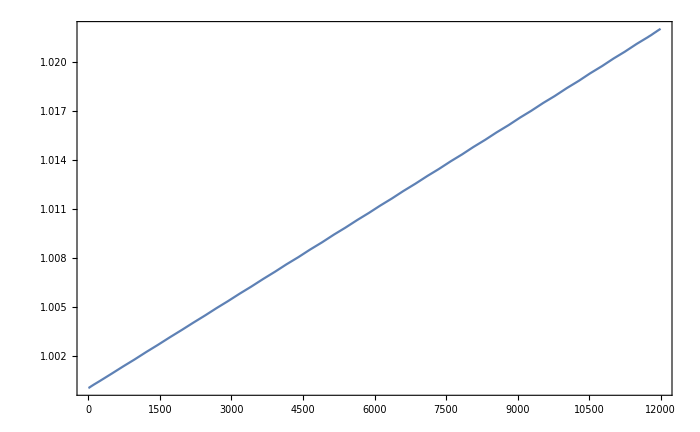

```mathematica
waveCW[x_]={waveCW1[x],waveCW2[x]};
solCW=NDSolve[{I D[waveCW[x],x]==hamilPR[x].waveCW[x],waveCW[0]==initCW},waveCW[x],{x,0,endpointCW}];
pltNorm[solCW,waveCW1,waveCW2,0,endpointCW]
```

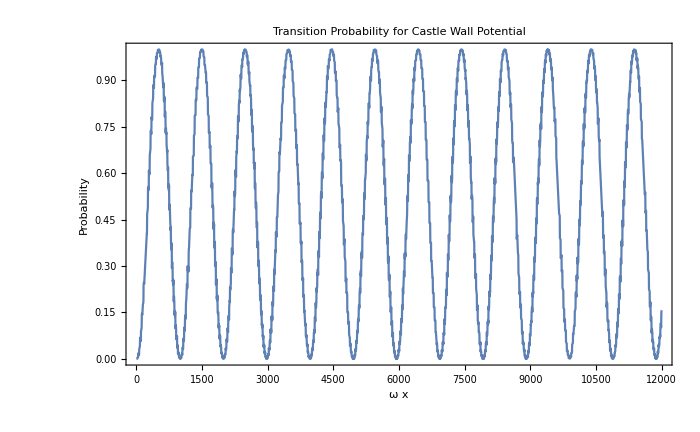

```mathematica
pltProbCW=pltProb[solCW,waveCW2,waveCW1,0,endpointCW,"Transition Probability for Castle Wall Potential",{"ω x","Probability"}]
```

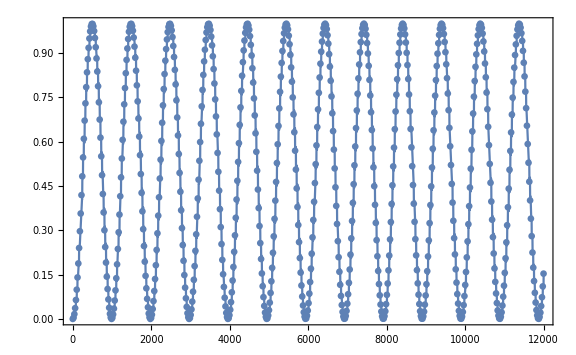

```mathematica
Show[cwTh,pltProbCW,ImageSize->Large,Frame->True]
```

Compare theoretical and numerical

```mathematica
probabilityCWNum[x_]=Evaluate[Abs[waveCW2[x]]^2/(Abs[waveCW1[x]]^2+Abs[waveCW2[x]]^2)/.solCW[[1]]];
Grid[Table[{probabilityCWTh[n],probabilityCWNum[n*Total[periodscw]],ScientificForm[(probabilityCWTh[n]-probabilityCWNum[n*Total[periodscw]])/probabilityCWTh[n]]},{n,0,100}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

0. | 0. | Indeterminate
0.00409504 | 0.00409501 | 7.22852×10^-6
0.0163131 | 0.016313 | 7.1463×10^-6
0.036454 | 0.0364537 | 7.05173×10^-6
0.0641878 | 0.0641874 | 6.93385×10^-6
0.0990603 | 0.0990597 | 6.79432×10^-6
0.1405 | 0.140499 | 6.63553×10^-6
0.187829 | 0.187828 | 5.10077×10^-6
0.240271 | 0.240269 | 6.26684×10^-6
0.296967 | 0.296966 | 4.76813×10^-6
0.35699 | 0.356987 | 5.83459×10^-6
0.419354 | 0.419352 | 4.38966×10^-6
0.48304 | 0.483037 | 5.33825×10^-6
0.547003 | 0.547001 | 5.06421×10^-6
0.610197 | 0.610195 | 3.73109×10^-6
0.671585 | 0.671582 | 4.45907×10^-6
0.730163 | 0.73016 | 4.12454×10^-6
0.784971 | 0.784968 | 3.76669×10^-6
0.835111 | 0.835108 | 3.38274×10^-6
0.879762 | 0.879759 | 2.97004×10^-6
0.918192 | 0.91819 | 2.52553×10^-6
0.949772 | 0.94977 | 2.04561×10^-6
0.973985 | 0.973984 | 1.52664×10^-6
0.990434 | 0.990433 | 9.63264×10^-7
0.998849 | 0.998849 | 3.50074×10^-7
0.999094 | 0.999094 | -2.86887×10^-7
0.991163 | 0.991164 | -9.20609×10^-7
0.975186 | 0.975188 | -1.78212×10^-6
0.951427 | 0.951429 | -2.22911×10^-6
0.920272 | 0.920276 | -3.66893×10^-6
0.882234 | 0.882238 | -4.65333×10^-6
0.837934 | 0.837939 | -5.43166×10^-6
0.788099 | 0.788104 | -5.58843×10^-6
0.733545 | 0.73355 | -6.69879×10^-6
0.675166 | 0.675173 | -1.01126×10^-5
0.613917 | 0.613924 | -1.18916×10^-5
0.550802 | 0.55081 | -1.36781×10^-5
0.486855 | 0.486863 | -1.62477×10^-5
0.423124 | 0.423132 | -1.89665×10^-5
0.360651 | 0.360659 | -2.16513×10^-5
0.300462 | 0.30047 | -2.61732×10^-5
0.24354 | 0.243548 | -3.08985×10^-5
0.19082 | 0.190827 | -3.74266×10^-5
0.143164 | 0.14317 | -4.59235×10^-5
0.101353 | 0.101358 | -5.6391×10^-5
0.0660716 | 0.0660767 | -7.65107×10^-5
0.0378983 | 0.0379024 | -1.0873×10^-4
0.0172943 | 0.017297 | -1.57479×10^-4
0.00459703 | 0.00459894 | -4.14009×10^-4
0.0000145714 | 0.0000153118 | -5.08122×10^-2
0.00362194 | 0.00362169 | 7.05391×10^-5
0.0153601 | 0.0153586 | 9.42012×10^-5
0.0350367 | 0.0350335 | 9.1107×10^-5
0.0623294 | 0.0623249 | 7.16481×10^-5
0.0967913 | 0.096785 | 6.47916×10^-5
0.137858 | 0.13785 | 5.90029×10^-5
0.184856 | 0.184846 | 5.37879×10^-5
0.237017 | 0.237007 | 3.92011×10^-5
0.293485 | 0.293475 | 3.48669×10^-5
0.353336 | 0.353325 | 3.11486×10^-5
0.415589 | 0.415578 | 2.78987×10^-5
0.479225 | 0.479214 | 2.40061×10^-5
0.543202 | 0.54319 | 2.0764×10^-5
0.60647 | 0.606458 | 2.00806×10^-5
0.667995 | 0.667983 | 1.78875×10^-5
0.726768 | 0.726756 | 1.58194×10^-5
0.781826 | 0.781813 | 1.70608×10^-5
0.832268 | 0.832256 | 1.43679×10^-5
0.877268 | 0.877257 | 1.17828×10^-5
0.916087 | 0.916079 | 9.30933×10^-6
0.948092 | 0.948085 | 6.96558×10^-6
0.972756 | 0.972751 | 4.78251×10^-6
0.989677 | 0.989674 | 2.79706×10^-6
0.998576 | 0.998575 | 1.03131×10^-6
0.999309 | 0.99931 | -6.94059×10^-7
0.991863 | 0.991865 | -2.1161×10^-6
0.97636 | 0.976364 | -3.90802×10^-6
0.953055 | 0.95306 | -6.06334×10^-6
0.922328 | 0.922336 | -8.60033×10^-6
0.884683 | 0.884694 | -1.14859×10^-5
0.840738 | 0.84075 | -1.46802×10^-5
0.791211 | 0.791225 | -1.8159×10^-5
0.736914 | 0.73693 | -2.19205×10^-5
0.678736 | 0.678754 | -2.59876×10^-5
0.617631 | 0.617649 | -3.04071×10^-5
0.554598 | 0.554618 | -3.52509×10^-5
0.490672 | 0.490692 | -4.06197×10^-5
0.426898 | 0.426918 | -4.66495×10^-5
0.364322 | 0.364341 | -5.3525×10^-5
0.303968 | 0.303986 | -6.15023×10^-5
0.246825 | 0.246842 | -7.09503×10^-5
0.193829 | 0.193845 | -8.24293×10^-5
0.145848 | 0.145862 | -9.68494×10^-5
0.103668 | 0.10368 | -1.15826×10^-4
0.0679807 | 0.0679904 | -1.4257×10^-4
0.0393696 | 0.0393771 | -1.9159×10^-4
0.0183036 | 0.0183084 | -2.64519×10^-4
0.00512791 | 0.00513041 | -4.89009×10^-4
0.0000582847 | 0.0000586112 | -5.60148×10^-3
0.00317778 | 0.00317605 | 5.45425×10^-4
0.0144353 | 0.0144315 | 2.66456×10^-4

#### Test

```mathematica
test[x_]=Evaluate[Abs[waveCW2[x]]^2/(Abs[waveCW1[x]]^2+Abs[waveCW2[x]]^2)/.solCW[[1]]]
```

Abs[InterpolatingFunction[{{0., 12000.}}, <>][x]]^2/(Abs[InterpolatingFunction[{{0., 12000.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 12000.}}, <>][x]]^2)

```mathematica
test[80]
```

0.0328258

For a constant matter potential, we have period as

```mathematica
omegacw[[1]]
"wavelength is"<>ToString[2Pi/omegacw]
```

40.8116

wavelength is{0.153956, 1.64504}

```mathematica
Table[{num*(Total@periodscw),probabilityCWTh[num]},{num,0,Floor[endpointCW/(Total@periodscw)]}]/1.6145371037912535;
```

Amplitude of constant matter is given by

```mathematica
(Sin[2θv]/factcw[[1]])^2
```

0.000498411

```mathematica
factcwFun[omegamatter_]:={√((omegamatter[[1]])^2+1-2(omegamatter[[1]])Cos[2θv]),√((omegamatter[[2]])^2+1-2(omegamatter[[2]])Cos[2θv])};
phicwFun[omegamatter_,periods_]:=factcwFun[omegamatter]*periods/2;
iso3Fun[omegamatter_,periods_]:=-Sin[phicwFun[omegamatter,periods][[1]]]Cos[phicwFun[omegamatter,periods][[2]]](Cos[2θv]-omegamatter[[1]])/(factcwFun[omegamatter][[1]])-Cos[phicwFun[omegamatter,periods][[1]]]Sin[phicwFun[omegamatter,periods][[2]]](Cos[2θv]-omegamatter[[2]])/(factcwFun[omegamatter][[2]])
```

```mathematica
iso3Fun[{1.1*α0/2,0.9*α0/2},{0.937,0.937}]
```

-0.169359

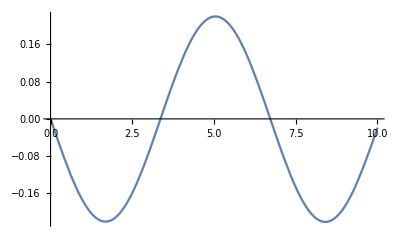

```mathematica
Plot[iso3Fun[{1.1*α0/2,0.9*α0/2},{x,x}],{x,0,10}]
```

```mathematica
FindRoot[iso3Fun[{1.1*α0/2,0.9*α0/2},{x,x}]==0,{x,3}]
```

{x→3.36388}

## Solving Each Equation in Vacuum Basis then Rotate

This problem can be solved in matter basis,hw

```mathematica
eqn1= I c1'[x]==Cos[2θv]/2(α0+α1 Cos[β x])c1[x]+Sin[2θv]/2(α0+α1 Cos[β x])c2[x]Exp[-I x]
eqn2=I c2'[x]==-Cos[2θv]/2(α0+α1 Cos[β x])c2[x]+ Sin[2θv]/2(α0+α1 Cos[β x])c1[x] Exp[I x]
```

ⅈ c1'[x]==0.206068 c1[x] (0.412135+0.0412135 Cos[1.00039 x])+0.455561 ⅇ^(-ⅈ x) c2[x] (0.412135+0.0412135 Cos[1.00039 x])

ⅈ c2'[x]==0.455561 ⅇ^(ⅈ x) c1[x] (0.412135+0.0412135 Cos[1.00039 x])-0.206068 c2[x] (0.412135+0.0412135 Cos[1.00039 x])

```mathematica
solVac=NDSolve[{eqn1,eqn2,c1[0]==initVac[[1]],c2[0]==initVac[[2]]},{c1,c2},{x,0,endpoint}]
```

{{c1→InterpolatingFunction[{{0., 12000.}}, <>],c2→InterpolatingFunction[{{0., 12000.}}, <>]}}

Check normalization

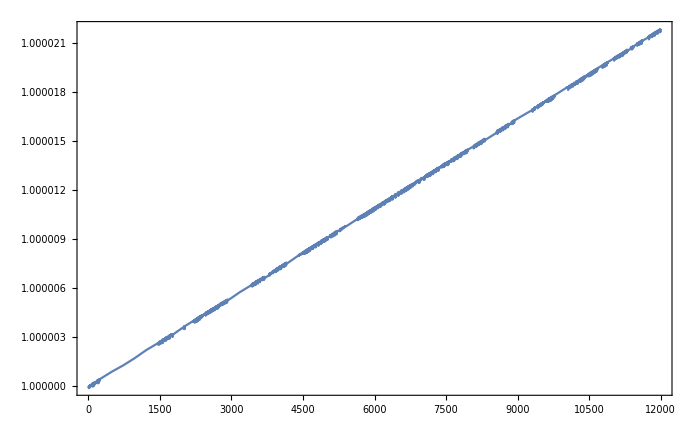

```mathematica
normVac=pltNorm[solVac,c1,c2,0,endpoint]
```

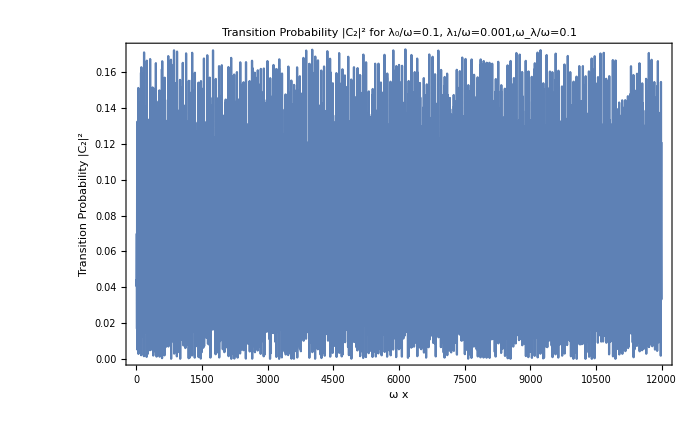

```mathematica
pltProb[solVac,c2,c1,0,endpoint,"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",{"ω x","Transition Probability |C_2|^2"}]
```

## Stimulated?

```mathematica
adiabProb[thetavA_,alpha0A_,alpha1A_,betaA_,xA_]:=((Sin[thetavA]^2)( Sin[xA/2]^2))/((alpha0A+alpha1A*Sin[betaA*xA])^2+1-2(alpha0A+alpha1A*Sin[betaA*xA])Cos[2thetavA])
```

```mathematica
adiabDeno[thetavA_,omegavA_,alpha0A_,alpha1A_,betaA_,xA_]:=(alpha0A+alpha1A*Sin[betaA*xA])^2+1-2(alpha0A+alpha1A*Sin[betaA*xA])Cos[2thetavA]
```

```mathematica
vacOscProb[thetavA_,omegavA_,xA_]:=(Sin[thetavA]^2)( Sin[xA/2]^2)
```

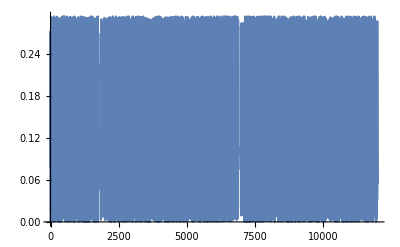

```mathematica
Plot[vacOscProb[θv,omegav,x],{x,0,endpoint}]
```

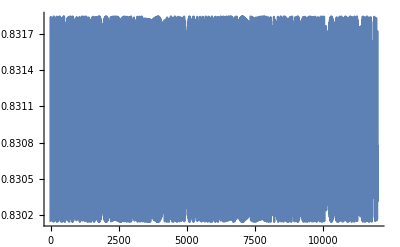

```mathematica
Plot[adiabDeno[θv,omegav,α0,α1,β,x],{x,0,endpoint}]
```

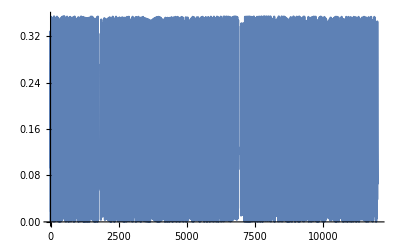

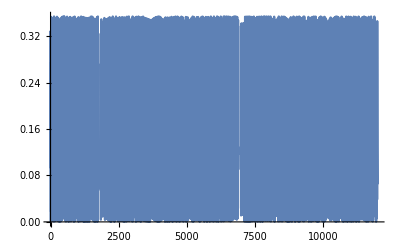

```mathematica
Plot[adiabProb[θv,α0,α1,β,x],{x,0,endpoint}]
Plot[adiabProb[θv,α0,0,β,x],{x,0,endpoint}]
```

## Temp

```mathematica
{{Cos[tv],-Sin[tv]},{Sin[tv],Cos[tv]}}.{{Cos[tm],Sin[tm]},{-Sin[tm],Cos[tm]}}//FullSimplify//MatrixForm
```

(Cos[tm-tv] | Sin[tm-tv]
-Sin[tm-tv] | Cos[tm-tv])

ListPlot::nonopt: Options expected (instead of {n, 0, 100}) beyond position 1 in -Abs[TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]][40 n]]^2/Abs[TagBox[InterpolatingFunction[« 5 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 1 »]]^2 + Abs[TagBox[InterpolatingFunction[« 5 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 1 »]]^2 + 0.0004983016780130461` Sin[0.5829217546409671` n]^2, {n, 0, 100}. An option must be a rule or a list of rules.

ListPlot[-(Abs[InterpolatingFunction[{{0., 12000.}}, <>][40 n]]^2/(Abs[InterpolatingFunction[{{0., 12000.}}, <>][40 n]]^2+Abs[InterpolatingFunction[{{0., 12000.}}, <>][40 n]]^2))+0.000498302 Sin[0.582922 n]^2,{n,0,100}]